Here is the given function

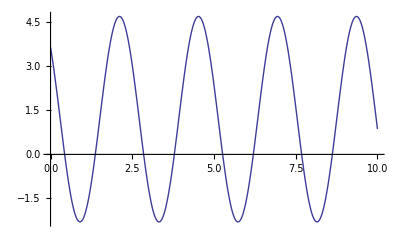

```mathematica
ff=1.2+3.5 Cos[2.6 t +.8];
Plot[ff,{t,0,10}]
```

I choose an observation time of 80 units, which I think (but don' t know) is sufficient and get my "experimental" data.
To analyze them I apply "Fourier" (that is exactly what I do with my real experimental data)

```mathematica
obstime=80;
ffdat=Table[ff,{t,0,obstime,.1}];
FT=Fourier[ffdat];
LT=Length[FT]
```

801

Following the hints in the web I extract the zero - frequency - term, which really yields a very good approximation to 1.2

```mathematica
a0=FT[[1]]/√LT//Chop
```

1.20639

To get an idea about the frequencies involved I plot a "spectrum". It has one peak, showing that only one frequency seems to be important (in my data there are several peaks)

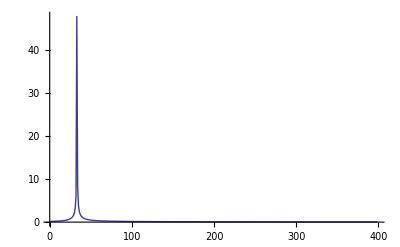

```mathematica
spec=ListLinePlot[Abs[Take[FT,{2,Floor[LT/2]}]],PlotRange->All]
```

I change the plot - region to find the peak more exactly and get it with "GetCoordinates" ( I found a "peakfinder" on a Wolfram-Site, but will not apply it here)

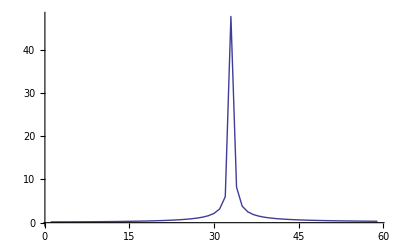

```mathematica
spec1=ListLinePlot[Abs[Take[FT,{2,60}]],PlotRange->All]
```

and here I have it. 0.5 is added for "rounding", 1 is added because I dropped the zero frequency (first) item in FT when plotting

```mathematica
peak=IntegerPart[#[[1]]+1.5]&/@{{33.08,47}}
```

{34}

and indeed, the frequency of 2.6 is very well approximated :

```mathematica
freq=N[(2π(#-1))/obstime]&/@peak
```

{2.59181}

The amplitude was given in a web site as

```mathematica
amp=(2 Abs[FT[[#]]])/(√LT)&/@peak
```

{3.37446}

and it is not really the 3.5 of the original function? How can I improve that?

Now it is said (with respect to "Fourier" of Mathematica) that one should extract the "phase" in this way:

```mathematica
phase=Arg[FT[[#]]]&/@peak
```

{-1.25514}

which is obviously not equl to 0.8. Ans when I after all these operations construct a - say - " inverse fourier function"  from the information obtained it is not "the real thing".

1.20639+3.37446 Cos[1.25514-2.59181 t]

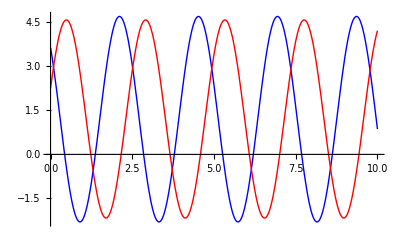

```mathematica
f1=a0+ amp[[1]]Cos[freq[[1]] t + phase[[1]]]
Plot[{ff,f1},{t,0,10},PlotStyle->{Blue,Red}]
```

Even shifting the "phase" about π (but I have no idea why I should do that)  make things a bit but not really better

1.20639+3.37446 Cos[1.88645+2.59181 t]

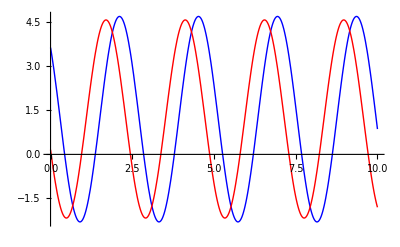

```mathematica
f2=a0+ amp[[1]]Cos[freq[[1]] t + phase[[1]]+ π]
Plot[{ff,f2},{t,0,10},PlotStyle->{Blue,Red}]
```

Of Course I could think now of a NonLinearFit to find an appropriate amplitude and phase, which indeed works quite well:

1.20639+3.49998 Cos[0.800054+2.6 t]

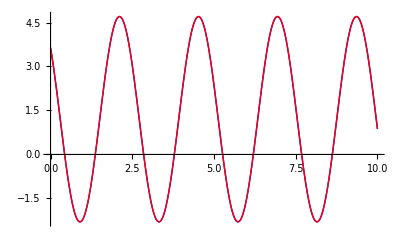

```mathematica
f3=NonlinearModelFit[Table[{t,ff},{t,0,obstime,.1}],a0+a1 Cos[ω t+φ],{{φ,π+phase[[1]]},{a1,amp[[1]]},{ω,freq[[1]]}},t]//Normal
Plot[{ff,f3},{t,0,10},PlotStyle->{Blue,Red}]
```

But I thought "Fourier" contained enough information to get a satisfactory approximation of the "experimental" data.

Now, after som Discussion with Daniel Lichtblau I constructed the following procedure to get the original function out of the "Fourier" data

```mathematica
invFT[peak_,ft_,data_,obstime_]:=Module[{},
LT=Length[ft];
a0=ft[[1]]/√LT//Chop;
freq=N[(2π (peak-1))/obstime];
amp2=Total[Exp[2π ⅈ  (peak-1)  Range[0,LT-1]/LT]data]/√LT;
amp=(2 Abs[amp2])/(√LT);
phase=-Arg[amp2];
{a0, amp  Cos[freq t +phase]}]
```

```mathematica
gg=Total[invFT[peak[[1]],FT,ffdat,obstime]]
```

1.20639+3.37446 Cos[1.25514+2.59181 t]

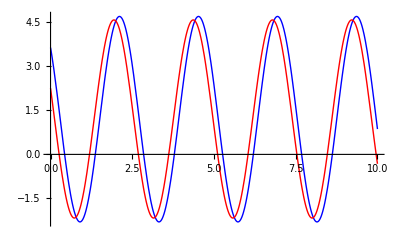

```mathematica
Plot[{ff,gg},{t,0,10},PlotStyle->{Blue,Red}]
```

```mathematica
(****************************************************************)
```

### 2 nd example

Another function, containing only ONE additional term

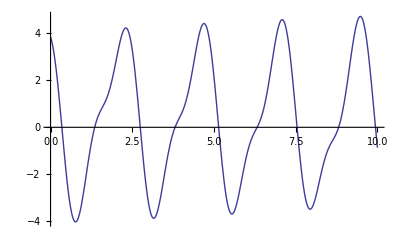

```mathematica
ff2=0.3+3.5 Cos[2.6 t +.8]+1.2 Cos[5.3 t -.4];
Plot[ff2,{t,0,10}]
```

"Observe" the signal and apply the same procedure as above

```mathematica
obstime=80;
ffdat2=Table[ff2,{t,0,obstime,.1}];
FT2=Fourier[ffdat2];
LT2=Length[FT2]
```

801

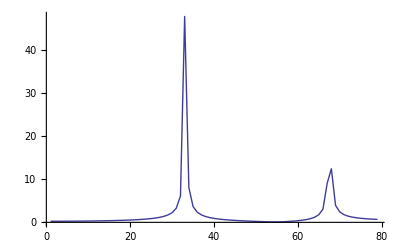

```mathematica
spec2=ListLinePlot[Abs[Take[FT2,{2,80}]],PlotRange->All]
```

```mathematica
peak2=IntegerPart[#[[1]]+1.5]&/@{{33.08,47.13},{68.04,11.57}}
```

{34,69}

```mathematica
freq=N[(2π(#-1))/obstime]&/@peak2
```

{2.59181,5.34071}

```mathematica
Length/@{FT2,ffdat2}
```

{801,801}

```mathematica
Amp2=Total[Exp[2π ⅈ  68  Range[0,LT-1]/LT]ffdat2]/√LT
(2 Abs[Amp2])/(√LT)
```

-2.27359+12.2491 ⅈ

0.880384

```mathematica
app2=invFT[#,FT2,ffdat2,obstime]&/@(peak2)
app3=app2[[1,1]]+Total[app2[[All,2]]]
```

{{0.308858,3.38294 Cos[1.25422+2.59181 t]},{0.308858,0.880384 Cos[1.75432-5.34071 t]}}

0.308858+0.880384 Cos[1.75432-5.34071 t]+3.38294 Cos[1.25422+2.59181 t]

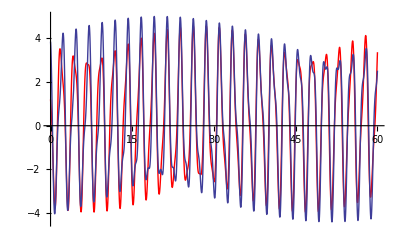

```mathematica
Show[Plot[app3,{t,0,60},PlotStyle->Red],Plot[ff2,{t,0,60}],PlotRange->All]
```

For comparison :

```mathematica
app3
ff2
```

0.308858+0.880384 Cos[1.75432-5.34071 t]+3.38294 Cos[1.25422+2.59181 t]

0.3+1.2 Cos[0.4-5.3 t]+3.5 Cos[0.8+2.6 t]